## Condiciones de regularidad Literatura

```mathematica
Clear[c]
fzprima=PowerExpand[1+(7 r^2)/(72 α)-(209 7^(2/3) r^(10/3))/(72 α (-2219 r^4+36 (-216 c α-216 α^2+√(53109 r^8+26628 r^4 α (c+α)+46656 α^2 (c+α)^2)))^(1/3))+1/(72 α)7^(1/3) r^(2/3) (-2219 r^4+36 (-216 c α-216 α^2+√(53109 r^8+26628 r^4 α (c+α)+46656 α^2 (c+α)^2)))^(1/3),Assumptions->{α>0,r>0}]
```

1+(7 r^2)/(72 α)-(209 7^(2/3) r^(10/3))/(72 α (-2219 r^4+36 (-216 c α-216 α^2+√(53109 r^8+26628 r^4 α (c+α)+46656 α^2 (c+α)^2)))^(1/3))+(7^(1/3) r^(2/3) (-2219 r^4+36 (-216 c α-216 α^2+√(53109 r^8+26628 r^4 α (c+α)+46656 α^2 (c+α)^2)))^(1/3))/(72 α)

### ¿Cómo se comporta f(r) cuando r tiende a Infinito?

```mathematica
FullSimplify[Assuming[r>0&& α>0 ,Simplify[Series[Simplify[fzprima],{r,Infinity,2}]]]]
```

Series::ztest: Unable to decide whether numeric quantities {-15533+756 √5901+108 7^(5/6) √843 (-2219+108 √5901)^(1/3)-2219 (7 (-2219+108 Power[«2»]))^(1/3)-209 (7 (-2219+108 Power[«2»]))^(2/3),7+(7 (-2219+108 √5901))^(1/3)-(209 (7 (-2219+108 Power[«2»]))^(2/3))/(-2219+108 √5901)} are equal to zero. Assuming they are.

1+(-c/3-α/3)/r^2+O[1/r]^(7/3)

```mathematica
Solve[Simplify[-c/3-α/3]==-μ,c]
```

{{c→-α+3 μ}}

```mathematica
c=Simplify[-3*((α/3)-μ)]
```

-α+3 μ

```mathematica
FullSimplify[Assuming[r>0&& α>0 ,Simplify[Series[Simplify[fzprima],{r,Infinity,2}]]]]
```

1-μ/r^2+O[1/r]^(7/3)

Ahora es asintóticamente plano

### ¿Cómo se comporta f(r) cuando r tiende a 0?

```mathematica
Assuming[r>0&& α>0&&μ>0,Simplify[Series[Simplify[fzprima],{r,0,2}]]]
```

1-((7^(1/3) μ) r^(2/3))/(2 (α μ)^(2/3))+(7 r^2)/(72 α)+O[r]^(7/3)

```mathematica
Expand[fzprima]
```

1+(7 r^2)/(72 α)-(209 7^(2/3) r^(10/3))/(72 α (-2219 r^4+36 (-216 α^2-216 α (-α+3 μ)+√(53109 r^8+79884 r^4 α μ+419904 α^2 μ^2)))^(1/3))+(7^(1/3) r^(2/3) (-2219 r^4+36 (-216 α^2-216 α (-α+3 μ)+√(53109 r^8+79884 r^4 α μ+419904 α^2 μ^2)))^(1/3))/(72 α)

### Reescalado

```mathematica
Clear[α]
fred=PowerExpand[FullSimplify[fzprima/.r->(Sqrt[(36*α)/7])*r2/.μ->α*μ2,Assumptions->α>0],Assumptions->α>0&&r2∈Reals&&μ2∈Reals]
```

1+r2^2/2-(209 r2^(10/3))/(2 7^(1/3) (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(1/3))+(r2^(2/3) (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(1/3))/(2 7^(2/3))

### Raíces de f(r)

### ¿Para qué valores de μ2 f(r) es finita?

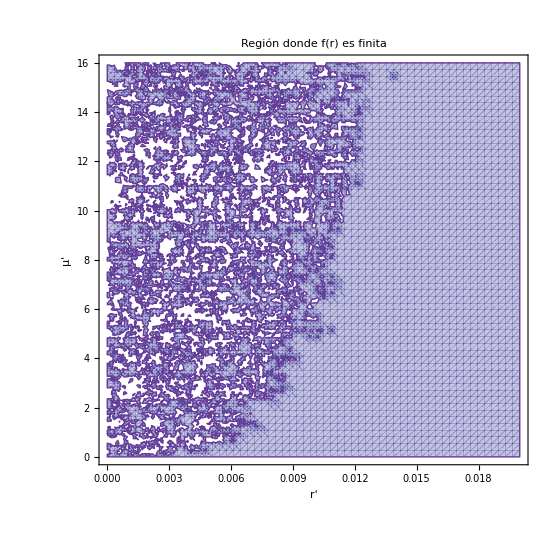

```mathematica
dem:=-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2)
ffinita=RegionPlot[dem!=0,{r2,0,0.02},{μ2,0,16},PlotPoints->60,Frame->True,FrameStyle->Directive[Black,1.6],FrameTicksStyle->Directive[Black,14],FrameLabel->{Style["r'",20,FontFamily->"Times",Bold],Style["μ'",20,FontFamily->"Times",Bold]},LabelStyle->Directive[16,FontFamily->"Times"],PlotLabel->Style["Región donde f(r) es finita",22,Bold,FontFamily->"Times"],ImageSize->550,PlotTheme->"Classic",BaseStyle->{FontFamily->"Times",16}]
```

```mathematica
Export["Regiones donde f es finita.png",ffinita]
```

Regiones donde f es finita.png

### Gráficas de f(r)

```mathematica
Plot3D[fred,{r2,0,3},{μ2,0,16},PlotRange->All,(*Color fijo usando una escala térmica continua*)ColorFunction->(ColorData["ThermometerColors"][#3]&),ColorFunctionScaling->True,(*Barra de color*)PlotLegends->BarLegend[{"ThermometerColors",{Min[fred],Max[fred]}}],(*Malla desactivada*)Mesh->None,PlotPoints->60,(*Gráficos más grandes*)AxesLabel->{Style["r₂",18,Bold],Style["μ₂",18,Bold],Style["f(r₂)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14]]
```

-Graphics3D-

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

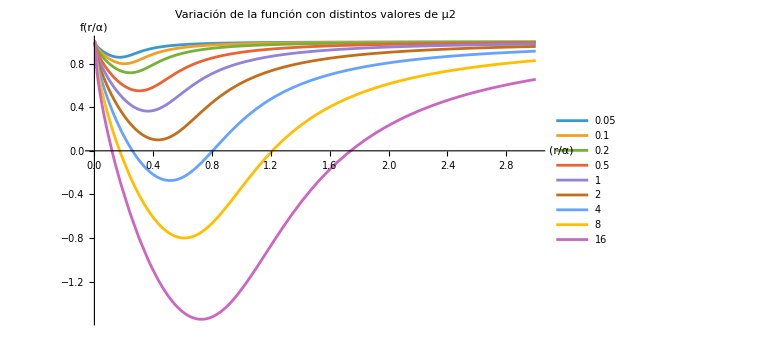

```mathematica
Plot[Evaluate@Table[fred,{μ2,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,3},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ2",AxesLabel->{Style["(r/α)",18,Bold],Style["f(r/α)",18,Bold],Style["f(r/α)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
```

### Invariante de Kretschman

```mathematica
NN[r2_]:=1
f[r2_]:=fred
Krt[r2_]=Assuming[r>0&&μ>0,FullSimplify[1/(r2^4 NN[r2]^2)(9 r2^4 f'[r2]^2 NN'[r2]^2+6 r2^4 NN[r2] f'[r2] NN'[r2] f''[r2]+NN[r2]^2 (12-24 f[r2]+12 f[r2]^2+6 r2^2 f'[r2]^2+r^4 f''[r2]^2)+12 r2^4 f[r2] f'[r2] NN'[r2] NN''[r2]+4 f[r2] NN[r] (3 r2^2 f'[r2] NN'[r2]+r2^4 f''[r2] NN''[r2])+4 f[r2]^2 (3 r2^2 NN'[r2]^2+r2^4 NN''[r2]^2))]]
```

3/49 (-2877+(7^(1/3) (274701 r2^(16/3)-12348 r2^(4/3) μ2+84 √7 r2^(4/3) √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2)-2926 7^(1/3) r2^4 (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(1/3)+7^(1/3) (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(4/3)))/(r2^(8/3) (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(2/3)))

```mathematica
Expand[Krt[r2]]
```

-1233/7+(117729 r2^(8/3))/(7^(2/3) (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(2/3))-(756 7^(1/3) μ2)/(r2^(4/3) (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(2/3))+(36 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))/(7^(1/6) r2^(4/3) (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(2/3))-(1254 r2^(4/3))/(7^(1/3) (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(1/3))+(3 (-2219 r2^4-882 μ2+6 √7 √(273132 r2^8+15533 r2^4 μ2+3087 μ2^2))^(2/3))/(7 7^(1/3) r2^(8/3))

Power::infy: Infinite expression 1/0.^(2/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

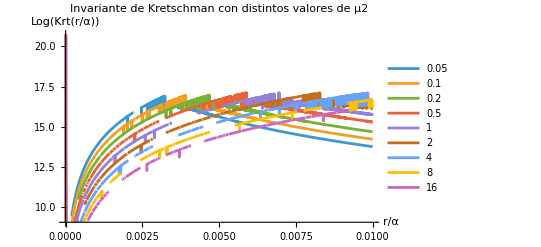

```mathematica
Plot[Evaluate@Table[Log[Krt[r2]],{μ2,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,0.01},PlotRange->Automatic,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Invariante de Kretschman con distintos valores de μ2",AxesLabel->{Style["r/α",18,Bold],Style["Log(Krt(r/α))",18,Bold],Style["Log(Krt(r/α))",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14]]
```

```mathematica
Assuming[r2>0&&μ2>0,Simplify[Series[Simplify[Krt[r2]],{r2,Infinity,2}]]]
```

Series::ztest1: Unable to decide whether numeric quantity -2877+(1512 7^(5/6) √843)/(-2219+108 √5901)^(2/3)+(274701 (7 (-2219+108 √5901))^(1/3))/(-2219+108 √5901)+(7 (-2219+108 √5901))^(2/3)-(2926 (7 (-2219+108 √5901))^(2/3))/(-2219+108 √5901) is equal to zero. Assuming it is.

O[1/r2]^(7/3)

```mathematica
Assuming[r2>0&&μ2>0,Simplify[Series[Simplify[Krt[r2]],{r2,0,2}]]]
```

(18 6^(1/3) μ2^(2/3))/r2^(8/3)-(6 (6^(2/3) μ2^(1/3)))/r2^(4/3)-1233/7+(1261 2^(1/3) r2^(4/3))/(7 3^(2/3) μ2^(1/3))+O[r2]^(7/3)

```mathematica
Simplify[(18 6^(1/3) μ2^(2/3))/r2^(8/3)-(6 (6^(2/3) μ2^(1/3)))/r2^(4/3)]
```

-(6 6^(1/3) (6^(1/3) r2^(4/3)-3 μ2^(1/3)) μ2^(1/3))/r2^(8/3)